# Relative degree

## Two mass system

```mathematica
ClearAll["Global`*"]
```

```mathematica
x=({{x1}, {x2}, {x3}, {x4}});
```

#### Equation of motion Mx’’ + B = Hu

```mathematica
M=({{m1, 0}, {0, m2}});
```

```mathematica
B=({{k, -k}, {-k, k}}).({{x3}, {x4}})+({{s, -s}, {-s, s}}).({{x1}, {x2}});
```

```mathematica
H=({{1}, {0}});
```

#### x’ = f(x) + g(x)u

```mathematica
inv=Inverse[M].(H u-B);
```

```mathematica
xdot ={{x3}, {x4},inv[[1]],inv[[2]]}
```

{{x3},{x4},{(u-s x1+s x2-k x3+k x4)/m1},{(s x1-s x2+k x3-k x4)/m2}}

```mathematica
gx=Coefficient[xdot,u]
```

{{0},{0},{1/m1},{0}}

```mathematica
fx=xdot-gx u//Simplify
```

{{x3},{x4},{(s (-x1+x2)+k (-x3+x4))/m1},{(s x1-s x2+k x3-k x4)/m2}}

### x1 output

```mathematica
hx=x1;
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{x3}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx
```

{{1/m1}}

#### ==> r=2

### x2 output

```mathematica
hx=x2;
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{x4}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx
```

{{0}}

#### L_g(L^2)_fh(x) k=2

```mathematica
Lf2hx=D[Lfhx,Transpose[x]].fx
```

{{(s x1-s x2+k x3-k x4)/m2}}

```mathematica
LgLf2hx=D[Lf2hx,Transpose[x]].gx
```

{{{k/(m1 m2)}}}

#### ==> r=3

## Cart pole system

```mathematica
ClearAll["Global`*"]
```

```mathematica
x=({{x1}, {x2}, {x3}, {x4}});
```

#### Equation of motion Mx’’ + B = Hu

```mathematica
M=({{m1+m2, m2 l Cos[x2]}, {m2 l Cos[x2], m2 l^2}});
```

```mathematica
B=({{0}, {-m2 l x4^2 Sin[x2]+m2 g l Sin[x2]}});
```

```mathematica
H=({{1}, {0}});
```

#### x’ = f(x) + g(x)u

```mathematica
inv=Inverse[M].(H u-B);
```

```mathematica
xdot ={{x3}, {x4},inv[[1]],inv[[2]]};
```

```mathematica
gx=Coefficient[xdot,u]
```

{{0},{0},{(l^2 m2)/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)},{-(l m2 Cos[x2])/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)}}

```mathematica
fx=xdot-gx u//Simplify
```

{{x3},{x4},{-(m2 (-g+x4^2) Cos[x2] Sin[x2])/(m1+m2-m2 Cos[x2]^2)},{-((m1+m2) (g-x4^2) Sin[x2])/(l (m1+m2-m2 Cos[x2]^2))}}

### Cart position output

```mathematica
hx=x1;
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{x3}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx
```

{{(l^2 m2)/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)}}

```mathematica
LgLfhx/.x2->0
```

{{1/m1}}

#### ==> r=2

### Pole x coordinate output

```mathematica
hx=x1+l Sin[x2];
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{x3+l x4 Cos[x2]}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx
```

{{(l^2 m2)/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)-(l^2 m2 Cos[x2]^2)/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)}}

```mathematica
LgLfhx/.x2->0
```

{{0}}

#### ==> r=2 if φ ≠ 0 + kπ

#### L_g(L^2)_fh(x) k=2

```mathematica
Lf2hx=D[Lfhx,Transpose[x]].fx
```

{{-l x4^2 Sin[x2]-((m1+m2) (g-x4^2) Cos[x2] Sin[x2])/(m1+m2-m2 Cos[x2]^2)-(m2 (-g+x4^2) Cos[x2] Sin[x2])/(m1+m2-m2 Cos[x2]^2)}}

```mathematica
LgLf2hx=D[Lf2hx,Transpose[x]].gx
```

{{{-(l m2 Cos[x2] (-2 l x4 Sin[x2]-(2 m2 x4 Cos[x2] Sin[x2])/(m1+m2-m2 Cos[x2]^2)+(2 (m1+m2) x4 Cos[x2] Sin[x2])/(m1+m2-m2 Cos[x2]^2)))/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)}}}

```mathematica
LgLf2hx/.x2->0
```

{{{0}}}

#### L_g(L^3)_fh(x) k=3

```mathematica
Lf3hx=D[Lf2hx,Transpose[x]].fx;
```

```mathematica
LgLf3hx=D[Lf3hx,Transpose[x]].gx;
```

```mathematica
LgLf3hx/.x2->0//FullSimplify
```

{{{{(g+3 (-1+l) x4^2)/(l m1)}}}}

```mathematica
Solve[(g+3 (-1+l) x4^2)/(l m1)==0,x4]
```

{{x4→-(√g)/(√3 √(1-l))},{x4→(√g)/(√3 √(1-l))}}

#### ==> r=4 if φ = 0 + kπ and φ’ ≠ ± (√g)/(√3 √(1-l))

#### L_g(L^4)_fh(x) k=4

```mathematica
Lf4hx=D[Lf3hx,Transpose[x]].fx;
```

```mathematica
LgLf4hx=D[Lf4hx,Transpose[x]].gx;
```

```mathematica
LgLf4hx/.x2->0//FullSimplify
```

{{{{{0}}}}}

#### ==> r=5 if φ = 0 + kπ and φ’ = ± (√g)/(√3 √(1-l))

## Space robot

```mathematica
ClearAll["Global`*"]
```

```mathematica
x=({{q0[t]}, {q1[t]}, {q2[t]}, {q0'[t]}, {q1'[t]}, {q2'[t]}});
```

#### Equation of motion Mx’’ + C = Hu

### Elements of Mass Matrix

```mathematica
m11=1/(4 (m0+m1+m2))(4 I0 m0+4 I1 m0+4 I2 m0+4 I0 m1+4 I1 m1+4 I2 m1+4 l0^2 m0 m1+l1^2 m0 m1+4 I0 m2+4 I1 m2+4 I2 m2+4 l0^2 m0 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+4 l0 l1 m0 (m1+2 m2) Cos[fi0-q1[t]]+4 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+4 l1 l2 m0 m2 Cos[q2[t]]+2 l1 l2 m1 m2 Cos[q2[t]]);
```

```mathematica
m12=1/(4 (m0+m1+m2))(4 I1 m0+4 I2 m0+4 I1 m1+4 I2 m1+l1^2 m0 m1+4 I1 m2+4 I2 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+2 l0 l1 m0 (m1+2 m2) Cos[fi0-q1[t]]+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+4 l1 l2 m0 m2 Cos[q2[t]]+2 l1 l2 m1 m2 Cos[q2[t]]);
```

```mathematica
m13=1/(4 (m0+m1+m2))(4 I2 m0+4 I2 m1+4 I2 m2+l2^2 m0 m2+l2^2 m1 m2+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+l1 l2 (2 m0+m1) m2 Cos[q2[t]]);
```

```mathematica
m21=1/(4 (m0+m1+m2))(4 I1 m0+4 I2 m0+4 I1 m1+4 I2 m1+l1^2 m0 m1+4 I1 m2+4 I2 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+2 l0 l1 m0 (m1+2 m2) Cos[fi0-q1[t]]+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+4 l1 l2 m0 m2 Cos[q2[t]]+2 l1 l2 m1 m2 Cos[q2[t]]);
```

```mathematica
m22=1/(4 (m0+m1+m2))(4 I2 m0+4 I2 m1+l1^2 m0 m1+4 I2 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+4 I1 (m0+m1+m2)+2 l1 l2 (2 m0+m1) m2 Cos[q2[t]]);
```

```mathematica
m23=(l2^2 (m0+m1) m2+4 I2 (m0+m1+m2)+l1 l2 (2 m0+m1) m2 Cos[q2[t]])/(4 (m0+m1+m2));
```

```mathematica
m31=1/(4 (m0+m1+m2))(4 I2 m0+4 I2 m1+4 I2 m2+l2^2 m0 m2+l2^2 m1 m2+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+l1 l2 (2 m0+m1) m2 Cos[q2[t]]);
```

```mathematica
m32=(l2^2 (m0+m1) m2+4 I2 (m0+m1+m2)+l1 l2 (2 m0+m1) m2 Cos[q2[t]])/(4 (m0+m1+m2));
```

```mathematica
m33=(l2^2 (m0+m1) m2+4 I2 (m0+m1+m2))/(4 (m0+m1+m2));
```

### Elements of C Matrix

```mathematica
c1=1/(4 (m0+m1+m2))(2 l0 m0 (l1 (m1+2 m2) Sin[fi0-q1[t]]+l2 m2 Sin[fi0-q1[t]-q2[t]]) q1'[t]^2-2 l2 m2 (-2 l0 m0 Sin[fi0-q1[t]-q2[t]]+l1 (2 m0+m1) Sin[q2[t]]) q1'[t] q2'[t]-l2 m2 (-2 l0 m0 Sin[fi0-q1[t]-q2[t]]+l1 (2 m0+m1) Sin[q2[t]]) q2'[t]^2+q0'[t] (4 l0 m0 (l1 (m1+2 m2) Sin[fi0-q1[t]]+l2 m2 Sin[fi0-q1[t]-q2[t]]) q1'[t]-2 l2 m2 (-2 l0 m0 Sin[fi0-q1[t]-q2[t]]+l1 (2 m0+m1) Sin[q2[t]]) q2'[t]));
```

```mathematica
c2=-1/(4 (m0+m1+m2))(2 l0 m0 (l1 (m1+2 m2) Sin[fi0-q1[t]]+l2 m2 Sin[fi0-q1[t]-q2[t]]) q0'[t]^2+2 l1 l2 (2 m0+m1) m2 Sin[q2[t]] q0'[t] q2'[t]+l1 l2 (2 m0+m1) m2 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]));
```

```mathematica
c3=1/(4 (m0+m1+m2))l2 m2 ((-2 l0 m0 Sin[fi0-q1[t]-q2[t]]+l1 (2 m0+m1) Sin[q2[t]]) q0'[t]^2+2 l1 (2 m0+m1) Sin[q2[t]] q0'[t] q1'[t]+l1 (2 m0+m1) Sin[q2[t]] q1'[t]^2);
```

```mathematica
M=({{m11, m12, m13}, {m21, m22, m23}, {m31, m32, m33}});
```

```mathematica
B=({{c1}, {c2}, {c3}});
```

```mathematica
H=({{0, 0}, {1, 0}, {0, 1}});
u=({{u1}, {u2}});
```

#### x’ = f(x) + g(x)u

```mathematica
inv=Inverse[M].(H .u-B);
```

```mathematica
xdot ={x[[4]], x[[5]],x[[6]],inv[[1]],inv[[2]],inv[[3]]};
```

```mathematica
m0=40;m1=4;m2=3;I0=6.667;I1=0.333;I2=0.25;l0=1;l1=1;l2=1;fi0=Pi/6;
```

## u1 input

```mathematica
gx=Coefficient[xdot,u1]//Simplify ;
```

```mathematica
fx=xdot-gx u1//Simplify//Chop;
```

### End effector x coordinate

```mathematica
hx=1/(2 (m0+m1+m2))(2 l0 m0 Cos[fi0+q0[t]]+l1 (2 m0+m1) Cos[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]]);
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{1/94 (-80 Sin[π/6+q0[t]]-84 Sin[q0[t]+q1[t]]-91 Sin[q0[t]+q1[t]+q2[t]]) q0'[t]+1/94 (-84 Sin[q0[t]+q1[t]]-91 Sin[q0[t]+q1[t]+q2[t]]) q1'[t]-91/94 Sin[q0[t]+q1[t]+q2[t]] q2'[t]}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx//Simplify//Chop;
```

```mathematica
SetOptions[ContourPlot3D,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,FontWeight->Bold}];
```

```mathematica
ContourPlot3D[LgLfhx==0,{q0[t],0,2 Pi},{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2]}]
```

-Graphics3D-

```mathematica
subs=LgLfhx/.{q0[t]->0}//Simplify//Chop
s0=0;
```

{{(0.00234311-0.00227392 Cos[q1[t]]-0.00137849 Cos[2 q1[t]]-0.0289483 Cos[2 q2[t]]-0.0169954 Cos[2 (q1[t]+q2[t])]-0.0477524 Cos[3 q1[t]+2 q2[t]]+0.104375 Sin[q1[t]]+0.00238762 Sin[2 q1[t]]-0.05014 Sin[2 q2[t]]+0.0294369 Sin[2 (q1[t]+q2[t])]-0.377719 Sin[q1[t]+2 q2[t]]+0.0275698 Sin[3 q1[t]+2 q2[t]])/(-1.52376+0.144413 Cos[2 q1[t]]+0.446649 Cos[2 q2[t]]-0.0157621 Cos[2 (q1[t]+q2[t])]+0.250131 Sin[2 q1[t]]-0.0273007 Sin[2 (q1[t]+q2[t])])}}

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,FontWeight->Bold}];
```

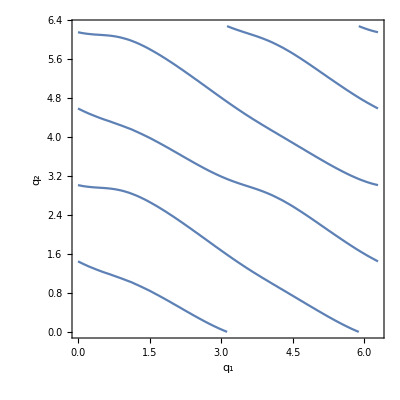

```mathematica
ContourPlot[subs==0,{q1[t],0,2 Pi},{q2[t],0,2 Pi},FrameLabel->{Subscript[q, 1],Subscript[q, 2]}]
```

```mathematica
subs2=subs/.{q1[t]->0}//Simplify
s1=0;
```

{{(-0.00130931-0.0936961 Cos[2 q2[t]]-0.370852 Sin[2 q2[t]])/(-1.37935+0.430887 Cos[2 q2[t]]-0.0273007 Sin[2 q2[t]])}}

```mathematica
sol=NSolve[subs2==0,q2[t]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{q2[t]→-1.69282},{q2[t]→-0.125447},{q2[t]→1.44877},{q2[t]→3.01615}}

```mathematica
val=q2[t]/.sol
```

{-1.69282,-0.125447,1.44877,3.01615}

```mathematica
val[[1]]=2*Pi+val[[1]]
val[[2]]=2*Pi+val[[2]]
```

4.59036

6.15774

```mathematica
Pi/2.
```

1.5708

```mathematica
s2=val[[4]];
```

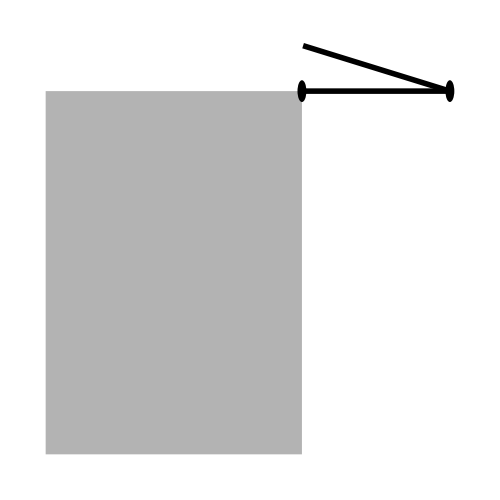

```mathematica
q0=s0; q1=s1; q2=s2;
Graphics[{GrayLevel[0.70],Thickness[0.008], Polygon[{{0,0},
                                                {+2l0 Cos[fi0] Cos[q0],2l0 Cos[fi0] Sin[q0]},
                                                {+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                               {+2l0 Sin[fi0] Cos[q0+Pi/2],+2l0 Sin[fi0] Sin[q0+Pi/2]}}],
               Black,Thickness[0.008],Line[{{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                        {+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]}}],
                Black,Thickness[0.008],Line[{{+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]},
                                                       {+2l0 Cos[q0+fi0]+l1 Cos[q0+q1]+l2 Cos[q0+q1+q2],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]+l2 Sin[q0+q1+q2]}}],
Black,Disk[{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},0.03],
Black,Disk[{+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]},0.03]},
ImageSize->{500,500}]
```

```mathematica
Clear[q0,q1,q2];
```

#### ==> r>2 in these cases

#### L_g L_f^2h(x) k=2

```mathematica
Lf2hx=D[Lfhx,Transpose[x]].fx;
```

```mathematica
LgLf2hx=D[Lf2hx,Transpose[x]].gx;
```

```mathematica
subs=LgLf2hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->0}//Simplify//Chop
s3=0;
```

{{{-0.467988 q1'[t]-0.946035 q2'[t]}}}

Unset::norep: Assignment on Derivative for q1' not found.

Unset::norep: Assignment on Derivative for q2' not found.

Unset::norep: Assignment on Derivative for q1' not found.

General::stop: Further output of Unset :: norep will be suppressed during this calculation.

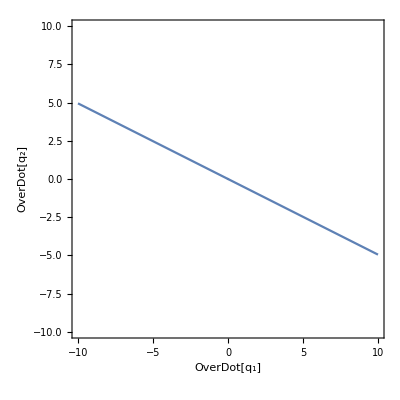

```mathematica
ContourPlot[subs==0,{q1'[t],-10,10},{q2'[t],-10,10},FrameLabel->{OverDot[Subscript[q, 1]],OverDot[Subscript[q, 2]]}]
```

```mathematica
sol=Solve[subs==0,{q1'[t],q2'[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{q2'[t]→0.-0.494684 q1'[t]}}

```mathematica
val2=q2'[t]/.sol
```

{0.-0.494684 q1'[t]}

```mathematica
s4=1; s5=val2/.q1'[t]->s4//First;
```

#### ==> r>3 in these cases

#### L_g L_f^3h(x) k=3

```mathematica
Lf3hx=D[Lf2hx,Transpose[x]].fx//Chop
```

{{{((1/47 (-84 Cos[q0[t]+q1[t]]-91 Cos[q0[t]+q1[t]+q2[t]]) q0'[t]+6+((-84 Sin[q0[t]+q1[t]]-91 Sin[1]) (1-1-1))/(94 (-2.65006+4+1.31564 1^2))) (1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+4+q2'[t] (q0'[t] (91/94 Sin[1] q0'[t]+1+1)+14+1)}}}
 |  |  |  |

```mathematica
LgLf3hx=D[Lf3hx,Transpose[x]].gx//Chop
```

{{{{((-0.9071-0.407032 Cos[q1[t]]+0.0945251 Cos[1/6 (1)]^2+0.198503 Cos[1/6 (π-6 1-6 1)] Cos[q2[t]]+0.104214 Cos[q2[t]]^2-0.235 Sin[q1[t]]) (1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+1/1+((1) (1))/(-2.65006+4+1)}}}}
 |  |  |  |

```mathematica
subs=LgLf3hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->s3,q1'[t]->s4,q2'[t]->s5}//Simplify//Chop
```

{{{{0.857058-4.13427 u2}}}}

```mathematica
val3=Solve[subs==0,u2]
```

{{u2→0.207306}}

```mathematica
s6=u2/.val3
```

{0.207306}

#### ==> r=4 if u2 != s6

#### L_g L_f^4h(x) k=4

```mathematica
Lf4hx=D[Lf3hx,Transpose[x]].fx
```

{{{{((1) (q2'[t] (91/94 Sin[q0[t]+q1[t]+q2[t]] q0'[t]+91/94 Sin[q0[t]+q1[t]+q2[t]] q1'[t]+91/94 Sin[q0[t]+q1[t]+q2[t]] q2'[t])+21+((1-1+1) 1)/(-2.65006+4+19 1)))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+4+q2'[t] (-1/(((11)^2)+10+1 1)}}}}
 |  |  |  |

```mathematica
LgLf4hx=D[Lf4hx,Transpose[x]].gx
```

{{{{{((-0.9071-0.407032 Cos[q1[t]]+0.0945251 Cos[1/6 (1)]^2+0.198503 Cos[1/6 (π-1-6 1)] Cos[q2[t]]+0.104214 Cos[q2[t]]^2-0.235 Sin[q1[t]]) (1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2+Cos[1/6 (1)] (1)-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+1/1+((1) 1)/1}}}}}
 |  |  |  |

```mathematica
subs=LgLf4hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->s3,q1'[t]->s4,q2'[t]->s5,u2->s6}//Simplify//Chop
```

{{{{{{2.57024}}}}}}

#### ==> r=5 if u2=s6

### End effector y coordinate

```mathematica
hx=(2 l0 m0 Sin[fi0+q0[t]]+l1 (2 m0+m1) Sin[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]])/(2 (m0+m1+m2));
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{1/94 (80 Cos[π/6+q0[t]]+84 Cos[q0[t]+q1[t]]+91 Cos[q0[t]+q1[t]+q2[t]]) q0'[t]+1/94 (84 Cos[q0[t]+q1[t]]+91 Cos[q0[t]+q1[t]+q2[t]]) q1'[t]+91/94 Cos[q0[t]+q1[t]+q2[t]] q2'[t]}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx//Simplify//Chop;
```

```mathematica
SetOptions[ContourPlot3D,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,FontWeight->Bold}];
```

```mathematica
ContourPlot3D[LgLfhx==0,{q0[t],0,2 Pi},{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2]}]
```

-Graphics3D-

```mathematica
subs=LgLfhx/.{q0[t]->0}//Simplify//Chop
s0=0;
```

{{(-0.00405838-0.10175 Cos[q1[t]]-0.00238762 Cos[2 q1[t]]+0.05014 Cos[2 q2[t]]-0.0294369 Cos[2 (q1[t]+q2[t])]+0.377719 Cos[q1[t]+2 q2[t]]-0.0275698 Cos[3 q1[t]+2 q2[t]]+0.00227392 Sin[q1[t]]-0.00137849 Sin[2 q1[t]]-0.0289483 Sin[2 q2[t]]-0.0169954 Sin[2 (q1[t]+q2[t])]-0.0477524 Sin[3 q1[t]+2 q2[t]])/(-1.52376+0.144413 Cos[2 q1[t]]+0.446649 Cos[2 q2[t]]-0.0157621 Cos[2 (q1[t]+q2[t])]+0.250131 Sin[2 q1[t]]-0.0273007 Sin[2 (q1[t]+q2[t])])}}

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,FontWeight->Bold}];
```

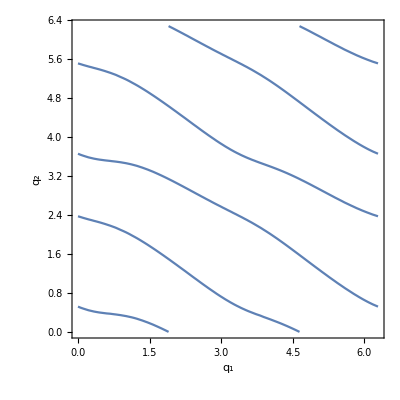

```mathematica
ContourPlot[subs==0,{q1[t],0,2 Pi},{q2[t],0,2 Pi},FrameLabel->{Subscript[q, 1],Subscript[q, 2]}]
```

```mathematica
subs2=subs/.{q1[t]->0}//Simplify
s1=0;
```

{{(-0.108196+0.370852 Cos[2 q2[t]]-0.0936961 Sin[2 q2[t]])/(-1.37935+0.430887 Cos[2 q2[t]]-0.0273007 Sin[2 q2[t]])}}

```mathematica
sol=NSolve[subs2==0,q2[t]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{q2[t]→-2.62332},{q2[t]→-0.765747},{q2[t]→0.518275},{q2[t]→2.37585}}

```mathematica
val=q2[t]/.sol
```

{-2.62332,-0.765747,0.518275,2.37585}

```mathematica
s2=val[[4]];
```

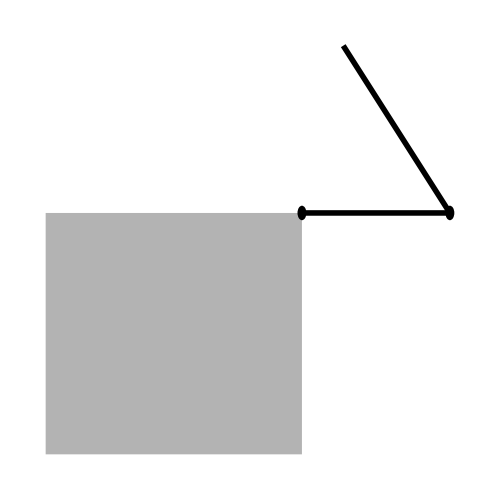

```mathematica
q0=s0; q1=s1; q2=s2;
Graphics[{GrayLevel[0.70],Thickness[0.008], Polygon[{{0,0},
                                                {+2l0 Cos[fi0] Cos[q0],2l0 Cos[fi0] Sin[q0]},
                                                {+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                               {+2l0 Sin[fi0] Cos[q0+Pi/2],+2l0 Sin[fi0] Sin[q0+Pi/2]}}],
               Black,Thickness[0.008],Line[{{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                        {+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]}}],
                Black,Thickness[0.008],Line[{{+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]},
                                                       {+2l0 Cos[q0+fi0]+l1 Cos[q0+q1]+l2 Cos[q0+q1+q2],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]+l2 Sin[q0+q1+q2]}}],
Black,Disk[{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},0.03],
Black,Disk[{+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]},0.03]},
ImageSize->{500,500}]
```

```mathematica
Clear[q0,q1,q2];
```

#### ==> r>2 in these cases

#### L_g L_f^2h(x) k=2

```mathematica
Lf2hx=D[Lfhx,Transpose[x]].fx;
```

```mathematica
LgLf2hx=D[Lf2hx,Transpose[x]].gx;
```

```mathematica
subs=LgLf2hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->0}//Simplify//Chop
s3=0;
```

{{{-0.238991 q1'[t]+0.50885 q2'[t]}}}

Unset::norep: Assignment on Derivative for q1' not found.

Unset::norep: Assignment on Derivative for q2' not found.

Unset::norep: Assignment on Derivative for q1' not found.

General::stop: Further output of Unset :: norep will be suppressed during this calculation.

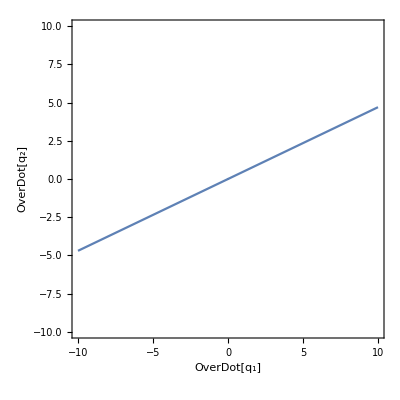

```mathematica
ContourPlot[subs==0,{q1'[t],-10,10},{q2'[t],-10,10},FrameLabel->{OverDot[Subscript[q, 1]],OverDot[Subscript[q, 2]]}]
```

```mathematica
sol=Solve[subs==0,{q1'[t],q2'[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{q2'[t]→0.+0.46967 q1'[t]}}

```mathematica
val2=q2'[t]/.sol
```

{0.+0.46967 q1'[t]}

```mathematica
s4=1; s5=val2/.q1'[t]->s4//First;
```

#### ==> r>3 in these cases

#### L_g L_f^3h(x) k=3

```mathematica
Lf3hx=D[Lf2hx,Transpose[x]].fx//Chop
```

{{{((1/47 (-84 Sin[q0[t]+q1[t]]-91 Sin[q0[t]+q1[t]+q2[t]]) q0'[t]+5+((84 Cos[q0[t]+q1[t]]+91 Cos[q0[t]+1+1]) (1))/(94 (-2.65006+4+1.31564 1^2))) (1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+4+q2'[t] (q0'[t] (-91/94 Cos[q0[t]+q1[t]+q2[t]] q0'[t]-1-1)+14+1)}}}
 |  |  |  |

```mathematica
LgLf3hx=D[Lf3hx,Transpose[x]].gx//Chop
```

{{{{((-0.9071-0.407032 Cos[q1[t]]+0.0945251 Cos[1/6 (1)]^2+0.198503 Cos[1/6 (π-6 1-6 1)] Cos[q2[t]]+0.104214 Cos[q2[t]]^2-0.235 Sin[q1[t]]) (1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+1/1+((1) (1))/(-2.65006+4+1)}}}}
 |  |  |  |

```mathematica
subs=LgLf3hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->s3,q1'[t]->s4,q2'[t]->s5}//Simplify//Chop
```

{{{{0.0114555+3.19335 u2}}}}

```mathematica
val3=Solve[subs==0,u2]
```

{{u2→-0.00358731}}

```mathematica
s6=u2/.val3
```

{-0.00358731}

#### ==> r=4 if u2 != s6

#### L_g L_f^4h(x) k=4

```mathematica
Lf4hx=D[Lf3hx,Transpose[x]].fx
```

{{{{((1) (q0'[t] (1/94 (-84 Cos[q0[t]+q1[t]]-91 Cos[q0[t]+q1[t]+q2[t]]) q0'[t]+1/94 (-84 Cos[q0[t]+q1[t]]-91 Cos[q0[t]+q1[t]+q2[t]]) q1'[t]-91/94 Cos[q0[t]+q1[t]+q2[t]] q2'[t])+21+((1) 1)/1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+(1) (1)+2+1+q2'[t] (-1/(1)^2+10+q2'[t] (1))}}}}
 |  |  |  |

```mathematica
LgLf4hx=D[Lf4hx,Transpose[x]].gx
```

{{{{{((-0.9071-0.407032 Cos[q1[t]]+0.0945251 Cos[1/6 (1)]^2+0.198503 Cos[1/6 (π-1-6 1)] Cos[q2[t]]+0.104214 Cos[q2[t]]^2-0.235 Sin[q1[t]]) (1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2+Cos[1/6 (1)] (1)-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+1/1+((1) 1)/1}}}}}
 |  |  |  |

```mathematica
subs=LgLf4hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->s3,q1'[t]->s4,q2'[t]->s5,u2->s6}//Simplify//Chop
```

{{{{{{-14.4408}}}}}}

#### ==> r=5 if u2=s6

## u2 input

```mathematica
gx=Coefficient[xdot,u2]//Simplify ;
```

```mathematica
fx=xdot-gx u2//Simplify//Chop;
```

### End effector x coordinate

```mathematica
hx=1/(2 (m0+m1+m2))(2 l0 m0 Cos[fi0+q0[t]]+l1 (2 m0+m1) Cos[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]]);
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{1/94 (-80 Sin[π/6+q0[t]]-84 Sin[q0[t]+q1[t]]-91 Sin[q0[t]+q1[t]+q2[t]]) q0'[t]+1/94 (-84 Sin[q0[t]+q1[t]]-91 Sin[q0[t]+q1[t]+q2[t]]) q1'[t]-91/94 Sin[q0[t]+q1[t]+q2[t]] q2'[t]}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx//Simplify//Chop;
```

```mathematica
SetOptions[ContourPlot3D,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,FontWeight->Bold}];
```

```mathematica
ContourPlot3D[LgLfhx==0,{q0[t],0,2 Pi},{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2]}]
```

-Graphics3D-

```mathematica
subs=LgLfhx/.{q0[t]->0}//Simplify//Chop
s0=0;
```

{{(0.00227392 Cos[q1[t]]-0.159175 Cos[q1[t]-q2[t]]+0.0182005 Cos[q1[t]+q2[t]]+0.159175 Cos[3 q1[t]+q2[t]]+0.0477524 Cos[3 q1[t]+2 q2[t]]-0.104375 Sin[q1[t]]-0.205866 Sin[q1[t]-q2[t]]+1.75805 Sin[q1[t]+q2[t]]-0.0918994 Sin[3 q1[t]+q2[t]]+0.377719 Sin[q1[t]+2 q2[t]]-0.0275698 Sin[3 q1[t]+2 q2[t]])/(-1.52376+0.144413 Cos[2 q1[t]]+0.446649 Cos[2 q2[t]]-0.0157621 Cos[2 (q1[t]+q2[t])]+0.250131 Sin[2 q1[t]]-0.0273007 Sin[2 (q1[t]+q2[t])])}}

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,FontWeight->Bold}];
```

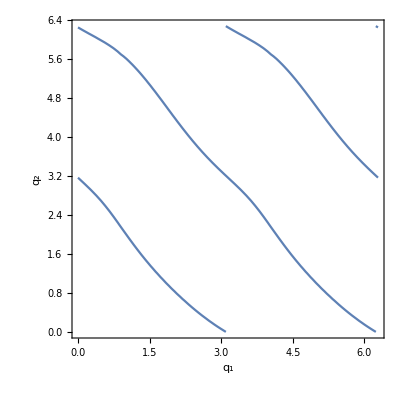

```mathematica
ContourPlot[subs==0,{q1[t],0,2 Pi},{q2[t],0,2 Pi},FrameLabel->{Subscript[q, 1],Subscript[q, 2]}]
```

```mathematica
subs2=subs/.{q1[t]->0}//Simplify
s1=0;
```

{{(0.00227392+0.0182005 Cos[q2[t]]+0.0477524 Cos[2 q2[t]]+1.87202 Sin[q2[t]]+0.350149 Sin[2 q2[t]])/(-1.37935+0.430887 Cos[2 q2[t]]-0.0273007 Sin[2 q2[t]])}}

```mathematica
sol=NSolve[subs2==0,q2[t],Reals]/.C[1]->0
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q2[t]→-3.11449},{q2[t]→-0.0265005}}

```mathematica
val=q2[t]/.sol
```

{-3.11449,-0.0265005}

```mathematica
s2=val[[2]];
```

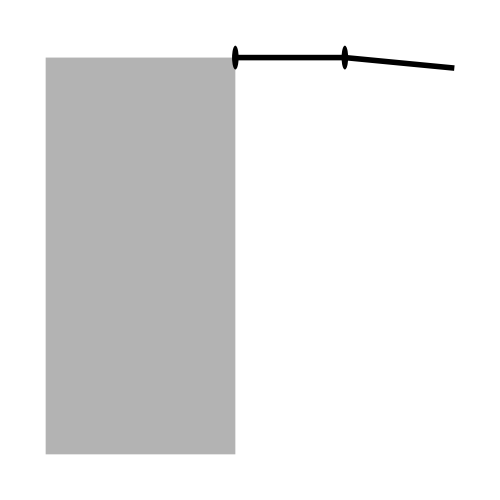

```mathematica
q0=s0; q1=s1; q2=s2;
Graphics[{GrayLevel[0.70],Thickness[0.008], Polygon[{{0,0},
                                                {+2l0 Cos[fi0] Cos[q0],2l0 Cos[fi0] Sin[q0]},
                                                {+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                               {+2l0 Sin[fi0] Cos[q0+Pi/2],+2l0 Sin[fi0] Sin[q0+Pi/2]}}],
               Black,Thickness[0.008],Line[{{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                        {+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]}}],
                Black,Thickness[0.008],Line[{{+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]},
                                                       {+2l0 Cos[q0+fi0]+l1 Cos[q0+q1]+l2 Cos[q0+q1+q2],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]+l2 Sin[q0+q1+q2]}}],
Black,Disk[{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},0.03],
Black,Disk[{+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]},0.03]},
ImageSize->{500,500}]
```

```mathematica
Clear[q0,q1,q2];
```

#### ==> r>2 in these cases

#### L_g L_f^2h(x) k=2

```mathematica
Lf2hx=D[Lfhx,Transpose[x]].fx;
```

```mathematica
LgLf2hx=D[Lf2hx,Transpose[x]].gx;
```

```mathematica
subs=LgLf2hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->0}//Simplify//Chop
s3=0;
```

{{{-3.12515 q1'[t]-5.43294 q2'[t]}}}

Unset::norep: Assignment on Derivative for q1' not found.

Unset::norep: Assignment on Derivative for q2' not found.

Unset::norep: Assignment on Derivative for q1' not found.

General::stop: Further output of Unset :: norep will be suppressed during this calculation.

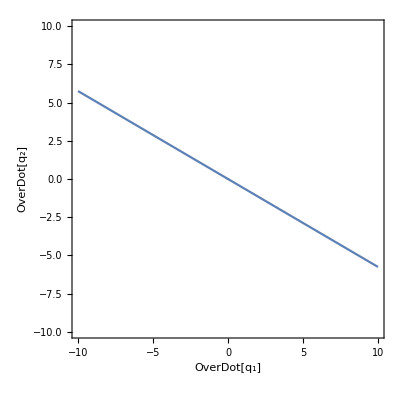

```mathematica
ContourPlot[subs==0,{q1'[t],-10,10},{q2'[t],-10,10},FrameLabel->{OverDot[Subscript[q, 1]],OverDot[Subscript[q, 2]]}]
```

```mathematica
sol=Solve[subs==0,{q1'[t],q2'[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{q2'[t]→0.-0.575223 q1'[t]}}

```mathematica
val2=q2'[t]/.sol
```

{0.-0.575223 q1'[t]}

```mathematica
s4=1; s5=val2/.q1'[t]->s4//First;
```

#### ==> r>3 in these cases

#### L_g L_f^3h(x) k=3

```mathematica
Lf3hx=D[Lf2hx,Transpose[x]].fx//Chop
```

{{{((1/47 (-84 Cos[q0[t]+q1[t]]-91 Cos[q0[t]+q1[t]+q2[t]]) q0'[t]+6+((-84 Sin[q0[t]+q1[t]]-91 Sin[1]) (1-1-1))/(94 (-2.65006+4+1.31564 1^2))) (1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+4+q2'[t] (q0'[t] (91/94 Sin[q0[t]+q1[t]+q2[t]] q0'[t]+1+1)+16+1)}}}
 |  |  |  |

```mathematica
LgLf3hx=D[Lf3hx,Transpose[x]].gx//Chop
```

{{{{((0.697185+6+0.1175 Sin[q1[t]]) (q2'[t] (91/94 Sin[q0[t]+q1[t]+q2[t]] q0'[t]+91/94 Sin[q0[t]+q1[t]+q2[t]] q1'[t]+91/94 Sin[q0[t]+q1[t]+q2[t]] q2'[t])+23+((1) 1)/1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+1/1+((-3.48049+5) 1)/(-2.65006+4+19 1)}}}}
 |  |  |  |

```mathematica
subs=LgLf3hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->s3,q1'[t]->s4,q2'[t]->s5}//Simplify//Chop
```

{{{{2.71401+9.62822 u1}}}}

```mathematica
val3=Solve[subs==0,u1]
```

{{u1→-0.281881}}

```mathematica
s6=u1/.val3
```

{-0.281881}

#### ==> r=4 if u1 != s6

#### L_g L_f^4h(x) k=4

```mathematica
Lf4hx=D[Lf3hx,Transpose[x]].fx
```

{{{{((1) (q2'[t] (91/94 Sin[q0[t]+q1[t]+q2[t]] q0'[t]+91/94 Sin[q0[t]+q1[t]+q2[t]] q1'[t]+91/94 Sin[q0[t]+q1[t]+q2[t]] q2'[t])+23+((1-1+1) 1)/(-2.65006+4+19 1)))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+4+q2'[t] (-1/(1)^2+12+q2'[t] (1))}}}}
 |  |  |  |

```mathematica
LgLf4hx=D[Lf4hx,Transpose[x]].gx
```

{{{{{((0.697185+6+0.1175 Sin[q1[t]]) (-((1) (1) (1))/(1)^2+21+q2'[t] (q0'[t] (1)+q1'[t] (1)+70+1+((1) 1)/1)))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2+Cos[1/6 (π-6 1-6 1)] 1-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+1/1+1/1}}}}}
 |  |  |  |

```mathematica
subs=LgLf4hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->s3,q1'[t]->s4,q2'[t]->s5,u1->s6}//Simplify//Chop
```

{{{{{{-20.4959}}}}}}

#### ==> r=5 if u2=s6

### End effector y coordinate

```mathematica
hx=(2 l0 m0 Sin[fi0+q0[t]]+l1 (2 m0+m1) Sin[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]])/(2 (m0+m1+m2));
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{1/94 (80 Cos[π/6+q0[t]]+84 Cos[q0[t]+q1[t]]+91 Cos[q0[t]+q1[t]+q2[t]]) q0'[t]+1/94 (84 Cos[q0[t]+q1[t]]+91 Cos[q0[t]+q1[t]+q2[t]]) q1'[t]+91/94 Cos[q0[t]+q1[t]+q2[t]] q2'[t]}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx//Simplify//Chop;
```

```mathematica
SetOptions[ContourPlot3D,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,FontWeight->Bold}];
```

```mathematica
ContourPlot3D[LgLfhx==0,{q0[t],0,2 Pi},{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2]}]
```

-Graphics3D-

```mathematica
subs=LgLfhx/.{q0[t]->0}//Simplify//Chop
s0=0;
```

{{(0.10175 Cos[q1[t]]+0.389665 Cos[q1[t]-q2[t]]-1.77907 Cos[q1[t]+q2[t]]+0.0918994 Cos[3 q1[t]+q2[t]]-0.377719 Cos[q1[t]+2 q2[t]]+0.0275698 Cos[3 q1[t]+2 q2[t]]-0.00227392 Sin[q1[t]]+0.159175 Sin[q1[t]-q2[t]]-0.0182005 Sin[q1[t]+q2[t]]+0.159175 Sin[3 q1[t]+q2[t]]+0.0477524 Sin[3 q1[t]+2 q2[t]])/(-1.52376+0.144413 Cos[2 q1[t]]+0.446649 Cos[2 q2[t]]-0.0157621 Cos[2 (q1[t]+q2[t])]+0.250131 Sin[2 q1[t]]-0.0273007 Sin[2 (q1[t]+q2[t])])}}

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,FontWeight->Bold}];
```

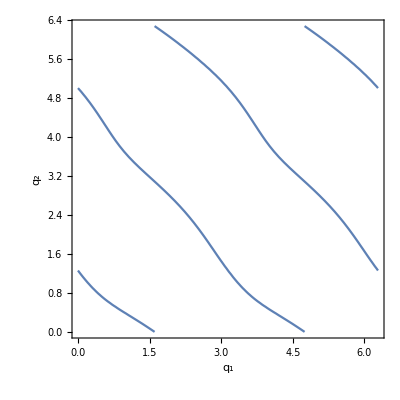

```mathematica
ContourPlot[subs==0,{q1[t],0,2 Pi},{q2[t],0,2 Pi},FrameLabel->{Subscript[q, 1],Subscript[q, 2]}]
```

```mathematica
subs2=subs/.{q1[t]->0}//Simplify
s1=0;
```

{{(0.10175-1.29751 Cos[q2[t]]-0.350149 Cos[2 q2[t]]-0.0182005 Sin[q2[t]]+0.0477524 Sin[2 q2[t]])/(-1.37935+0.430887 Cos[2 q2[t]]-0.0273007 Sin[2 q2[t]])}}

```mathematica
sol=NSolve[subs2==0,q2[t],Reals]/.C[1]->0
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q2[t]→-1.27212},{q2[t]→1.25995}}

```mathematica
val=q2[t]/.sol
```

{-1.27212,1.25995}

```mathematica
s2=val[[2]];
```

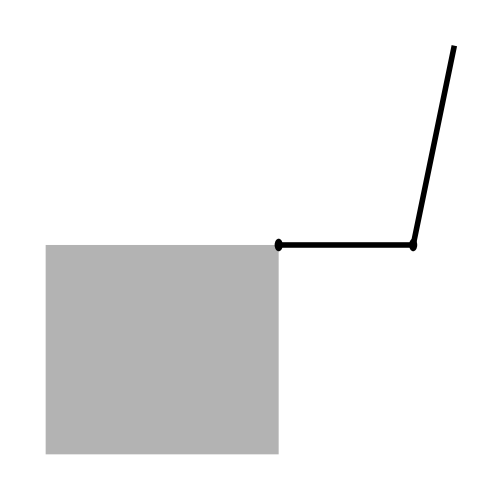

```mathematica
q0=s0; q1=s1; q2=s2;
Graphics[{GrayLevel[0.70],Thickness[0.008], Polygon[{{0,0},
                                                {+2l0 Cos[fi0] Cos[q0],2l0 Cos[fi0] Sin[q0]},
                                                {+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                               {+2l0 Sin[fi0] Cos[q0+Pi/2],+2l0 Sin[fi0] Sin[q0+Pi/2]}}],
               Black,Thickness[0.008],Line[{{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                        {+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]}}],
                Black,Thickness[0.008],Line[{{+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]},
                                                       {+2l0 Cos[q0+fi0]+l1 Cos[q0+q1]+l2 Cos[q0+q1+q2],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]+l2 Sin[q0+q1+q2]}}],
Black,Disk[{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},0.03],
Black,Disk[{+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]},0.03]},
ImageSize->{500,500}]
```

```mathematica
Clear[q0,q1,q2];
```

#### ==> r>2 in these cases

#### L_g L_f^2h(x) k=2

```mathematica
Lf2hx=D[Lfhx,Transpose[x]].fx;
```

```mathematica
LgLf2hx=D[Lf2hx,Transpose[x]].gx;
```

```mathematica
subs=LgLf2hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->0}//Simplify//Chop
s3=0;
```

{{{-2.27552 q1'[t]-4.02643 q2'[t]}}}

Unset::norep: Assignment on Derivative for q1' not found.

Unset::norep: Assignment on Derivative for q2' not found.

Unset::norep: Assignment on Derivative for q1' not found.

General::stop: Further output of Unset :: norep will be suppressed during this calculation.

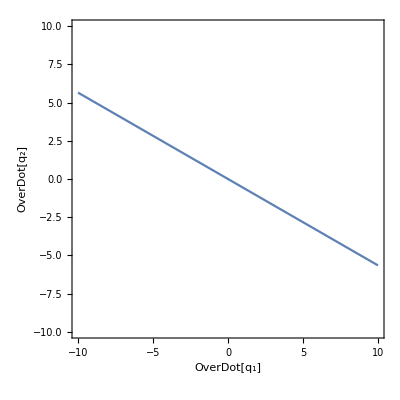

```mathematica
ContourPlot[subs==0,{q1'[t],-10,10},{q2'[t],-10,10},FrameLabel->{OverDot[Subscript[q, 1]],OverDot[Subscript[q, 2]]}]
```

```mathematica
sol=Solve[subs==0,{q1'[t],q2'[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{q2'[t]→0.-0.565145 q1'[t]}}

```mathematica
val2=q2'[t]/.sol
```

{0.-0.565145 q1'[t]}

```mathematica
s4=1; s5=val2/.q1'[t]->s4//First;
```

#### ==> r>3 in these cases

#### L_g L_f^3h(x) k=3

```mathematica
Lf3hx=D[Lf2hx,Transpose[x]].fx//Chop
```

{{{((1/47 (-84 Sin[q0[t]+q1[t]]-91 Sin[q0[t]+q1[t]+q2[t]]) q0'[t]+5+((84 Cos[q0[t]+q1[t]]+91 Cos[q0[t]+q1[t]+q2[t]]) (1))/(94 (-2.65006+4+1.31564 1^2))) (1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+4+q2'[t] (q0'[t] (-91/94 Cos[q0[t]+q1[t]+q2[t]] q0'[t]-1-91/94 Cos[1] q2'[t])+16+1)}}}
 |  |  |  |

```mathematica
LgLf3hx=D[Lf3hx,Transpose[x]].gx//Chop
```

{{{{((0.697185+0.203516 Cos[q1[t]]-0.0945251 Cos[1/6 (1)]^2+0.981512 1+0.330838 Cos[1/6 (π-6 1)] Cos[q2[t]]+Cos[1/6 (π-6 q1[t]-6 q2[t])] (1)+0.1175 Sin[q1[t]]) 1)/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+1/1+((1) (1))/1}}}}
 |  |  |  |

```mathematica
subs=LgLf3hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->s3,q1'[t]->s4,q2'[t]->s5}//Simplify//Chop
```

{{{{5.95981+6.46007 u1}}}}

```mathematica
val3=Solve[subs==0,u1]
```

{{u1→-0.922561}}

```mathematica
s6=u1/.val3
```

{-0.922561}

#### ==> r=4 if u1 != s6

#### L_g L_f^4h(x) k=4

```mathematica
Lf4hx=D[Lf3hx,Transpose[x]].fx
```

{{{{((1) (q0'[t] (1/94 (-84 Cos[q0[t]+q1[t]]-91 Cos[q0[t]+q1[t]+q2[t]]) q0'[t]+1/94 (-84 Cos[q0[t]+q1[t]]-91 Cos[q0[t]+q1[t]+q2[t]]) q1'[t]-91/94 Cos[q0[t]+q1[t]+q2[t]] q2'[t])+q1'[t] (1)+21+1+((1) 1)/1))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+4+q2'[t] (-1/1^2+12+q2'[t] (1))}}}}
 |  |  |  |

```mathematica
LgLf4hx=D[Lf4hx,Transpose[x]].gx
```

{{{{{((0.697185+6+0.1175 Sin[q1[t]]) (-((1) (1) (1))/(1)^2+21+q2'[t] (q0'[t] (1)+q1'[t] (1)+74+1+((1) 1)/1)))/(-2.65006+1. Cos[1/6 (π-6 q1[t])]^2+0.359298 Cos[1/6 (1)]^2+Cos[1/6 (π-6 1-6 1)]1(11-0.844693 Cos[1/6 (π-6 q1[t])] Cos[1/6 (π-6 q1[t]-6 q2[t])] Cos[q2[t]]+1.31564 Cos[q2[t]]^2)+1+1/1}}}}}
 |  |  |  |

```mathematica
subs=LgLf4hx/.{q0[t]->s0, q1[t]->s1, q2[t]->s2,q0'[t]->s3,q1'[t]->s4,q2'[t]->s5,u1->s6}//Simplify//Chop
```

{{{{{{-20.7467}}}}}}

#### ==> r=5 if u2=s6